```mathematica
(* Setup *)
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot,LogPlot,LogLinearPlot,ParametricPlot,ParametricPlot3D,SmoothHistogram},PlotStyle->ColorData[45,"ColorList"]];
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogPlot,LogPlot,LogLinearPlot,SmoothHistogram},FillingStyle->Directive[RGBColor[0.5,0.4,0.1]]];
SetOptions[{Plot,ListPlot,ListLinePlot,Plot3D,ListPlot3D,LogPlot,LogLinearPlot,ListLogPlot,ParametricPlot,ParametricPlot3D,TradingChart,CandlestickChart,SmoothHistogram},AxesStyle->Directive[GrayLevel[0.75],FontSize->11,FontFamily->"Ubuntu Mono"]];
SetOptions[{TradingChart,CandlestickChart},TrendStyle->{RGBColor[0,0.8,0],RGBColor[1,0.1,0]},FrameTicksStyle->Directive[GrayLevel[0.75],Dashed,FontSize->10,FontFamily->"Ubuntu Mono"],GridLinesStyle->Directive[GrayLevel[0.5],Dashed]];
```

## Mutual Information

```mathematica
frdata=Import[FileNameJoin[{NotebookDirectory[],"features/english_french.csv"}]];
dedata=Import["/Users/Vishesh/repos/alignment-tree/features/english_deutsch.csv"];
```

```mathematica
Discretize[val_] := If[Chop[val] == 0, 0, Ceiling[val^(1/2)] ]
FrequencyPad[one_, two_]:= Module[{hash1, hash2, intersect},
hash1=Hash[#1[[1]]]->#1&/@one;
hash2=Hash[#1[[1]]]->#1&/@two;
intersect= hash1[[;;,1]]~Intersection~hash2[[;;,1]];
Return[{intersect/.hash1, intersect/.hash2}];
];
MutualInformation[features_, featurelabels_, col_]:=Module[{yprob,xprob,xyprob1, xyprob0,i},
(*yprob = p(y), xprob = p(x), xyprob1 = p(x|y=1), xyprob0= p(x|y=0) *)
yprob = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[Gather[featurelabels[[;;]] ] ];
xprob = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[Gather[Discretize/@features[[;;, col]] ] ];
xyprob1 = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[
Gather[Select[Transpose[{featurelabels}~Join~{Discretize/@features[[;;,col]]}], #1[[1]]==1&][[;;,2]]]
];
xyprob0 = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[
Gather[Select[Transpose[{featurelabels}~Join~{Discretize/@features[[;;,col]]}], #1[[1]]==0&][[;;,2]]]
];
Return[  yprob[[2,2]] * (xyprob1[[;;,2]].Log@xyprob1[[;;,2]]-#1[[1,;;,2]].Log@#1[[2,;;,2]]&[ FrequencyPad[xyprob1, xprob] ]) +
yprob[[1,2]] * (xyprob0[[;;,2]].Log@xyprob0[[;;,2]]-#1[[1,;;,2]].Log@#1[[2,;;,2]]&[ FrequencyPad[xyprob0, xprob] ])];
];
```

```mathematica
SortBy[#,-#[[2]]&]&@Table[{#3[[c]],N@MutualInformation[#1~Join~#2,ConstantArray[1,Length@#1]~Join~ConstantArray[0,Length@#2],c]},{c,1,Length@#1[[1]]}]&[frdata[[2;;]],dedata[[2;;]],frdata[[1]]]//TableForm
```

flattened_num_nodes | 0.0796473
flattened_num_normal | 0.0636675
num_reverse | 0.0425243
flattened_depth | 0.0413429
depth | 0.0390398
flattened_num_reverse | 0.0371592
mean_height_from_leaf | 0.0336307
flattened_mean_height_from_leaf | 0.0267644
max_depth_reverse | 0.0233554
flattened_max_depth_reverse | 0.0231824
flattened_max_range_reverse | 0.0220475
max_range_reverse | 0.0220475
num_nodes | 0.0212747
num_normal | 0.0198571
flattened_min_range_reverse | 0.0172225
flattened_mean_range_reverse | 0.0171741
mean_range_reverse | 0.0171053
min_range_reverse | 0.0161768
flattened_length | 0.00454451
length | 0.00454451
min_height_tree_from_leaf | 0.00253578
flattened_min_height_tree_from_leaf | 0.00121683

## Logistic Regression

```mathematica
H[X_,θ_,hθ_] := Table[Sum[-X[[i,j]]X[[i,k]]hθ[X[[i]], θ](1-hθ[X[[i]], θ]),{i,1,Length[X]}], {j,1,Length[θ]},{k,1,Length[θ]}]
Delθ[X_,Y_,θ_,hθ_]:=Table[Sum[(Y[[i]]-hθ[X[[i]],θ])X[[i,j]],{i,1,Length[X]}],{j,1,Length[θ]}]
Newton[θ_,X_,Y_,hθ_]:= θ- Inverse[H[X,θ,hθ]].Delθ[X,Y,θ,hθ]
Newton[θ_,{X_,Y_,hθ_}]:= Newton[θ,X,Y,hθ]
```

```mathematica
Iterate[func_,n_,initial_,consts_]:=Module[{temp,i},
temp=initial;
For[i=0,i<n,i++,
 temp =func[temp,consts];
];
Return[temp];
];
```

```mathematica
XX=Table[Join[{1.},#[[i]]],{i,1,Length@#}]&@(hifeatures~Join~frfeatures);YY=ConstantArray[{1.}, Length@hifeatures]~Join~ConstantArray[{0.},Length@frfeatures];
```

```mathematica
Clear[sol]
sol[X_,Y_,θ_]:=Iterate[Newton, 100, θ, {X,Y,1/(1+ⅇ^(-#1.Flatten[#2]))&}]
```

```mathematica
sol[XX,YY,{0.,0.,0.}]
```

```mathematica
Show[
BubbleChart[{Flatten/@Tally@hifeatures,Flatten/@Tally@frfeatures}],
Plot[Solve[0.2542553502946426+-0.34731543843304x1+0.33441826042367423x2==0,x2][[1,1,2]],{x1,0,40},PlotStyle->Thick]
]
```

-Graphics-

```mathematica
Length@Select[0.2542553502946426+-0.34731543843304#[[1]]+0.33441826042367423#[[2]]&/@hifeatures,#>=0&]
```

69

## Density Based Estimation

```mathematica
Clear@denseclassifier
denseclassifier[p_:10,k_:1,w_:0.2]:=With[{mins=Min/@Transpose@#,maxs=Max/@Transpose@#},Show[
ContourPlot[Norm[Exp[-k Norm[{x,y}-#]]&/@#,p]/Norm[1&/@#,p],{x,mins[[1]]-(maxs-mins)[[1]]*w,maxs[[1]]+(maxs-mins)[[1]]*w},{y,mins[[2]]-(maxs-mins)[[2]]*w,maxs[[2]]+(maxs-mins)[[2]]*w},PlotLegends->Automatic,PlotRange->All, Contours->Table[0.05i,{i,0,20}],ColorFunction->"TemperatureMap"],
ListPlot[#]
]]&;
```

```mathematica
denseclassifier[][{{1,1},{3,4}}]
```

-Graphics-

```mathematica
hif[[1,{1,14}]]
```

{length,compressed_depth}

```mathematica
hif=Import[FileNameJoin[{NotebookDirectory[],"features/english_hindi.csv"}]];
frf=Import[FileNameJoin[{NotebookDirectory[],"features/english_french.csv"}]];
```

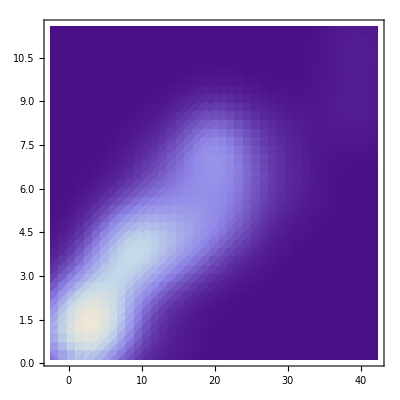

```mathematica
SmoothDensityHistogram@hif[[2;;,{1,14}]]
```

```mathematica
denseclassifier[10,2][hif[[2;;,{1,14}]]]
denseclassifier[10,2][frf[[2;;,{1,14}]]]
```

-Graphics-

-Graphics-

## Topological Data Analysis

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
clusterorder[dmat_]:=dmat[[ #,#]]&@ClusterFlatten@DirectAgglomerate[#,Linkage->"Ward"]&@dmat
```

```mathematica
dmat = DistanceMatrix@frf[[2;;]];
```

```mathematica
ArrayPlot[clusterorder@dmat,ColorFunction->Function[{z},GrayLevel[z^0.33]]]
```

-Graphics-

```mathematica
Juxt[fs_]:=Table[fs[[i]]@#,{i,1,Length[fs]}]&
```

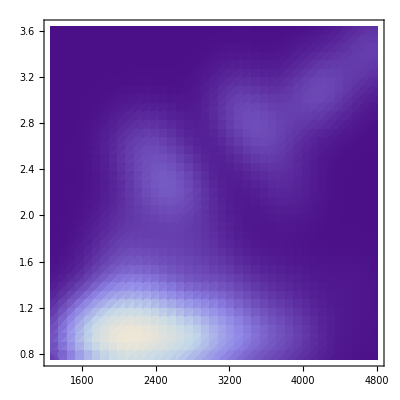

```mathematica
(* This is Cmax (max centrality). You can also use Mean, Geometric Mean, Harmonic Mean, etc *)
centrality[n_,distances_]:=Norm[distances,n] 
density[n_,k_,distances_]:=Norm[Exp[-k #]&/@distances,n]
SmoothDensityHistogram[Juxt[{centrality[Infinity,#]&,density[2,2,#]&}]/@dmat]
```